```mathematica
ComputeGraph[g_,vertexsets_]:=Block[{result, edge,a,b,vertices},
If[CompleteGraphQ[g],
result={g},
edge = First[EdgeList[GraphComplement[g]]];
a=edge[[1]];
b=edge[[2]];
vertices=DeleteDuplicates[Table[If[k==a||k==b,Join[vertexsets[[a]],vertexsets[[b]]],vertexsets[[k]]],{k,Length[vertexsets]}]];
result=Join[
ComputeGraph[Graph[VertexContract[g,{a,b}]],vertices],
ComputeGraph[Graph[EdgeAdd[g,edge]],vertexsets]
]
];
result
]
```

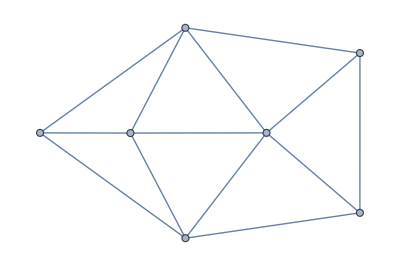

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->6,3<->6,4<->6,5<->6,7<->6,7<->2,7<->5,7<->1}]
```

Part::partw: Part 7 of {{1, 3}, {2, 6}, {4}, {5}, {7}} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 7 of {{1, 3}, {2}, {4}, {5}, {6}, {7}} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 7 of {{1, 4}, {2, 6}, {3}, {5}, {7}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

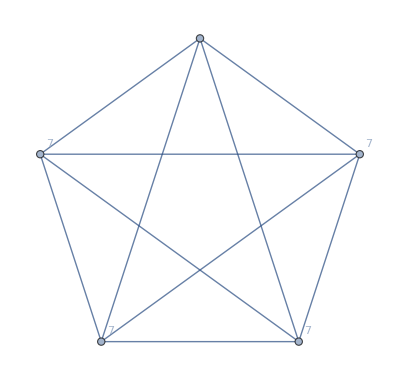
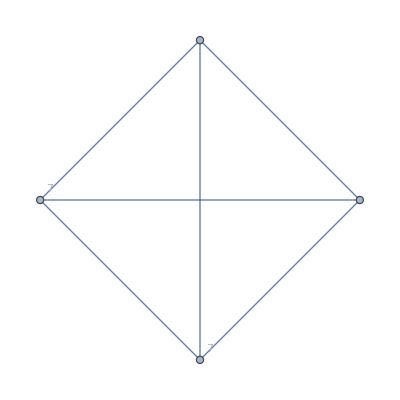
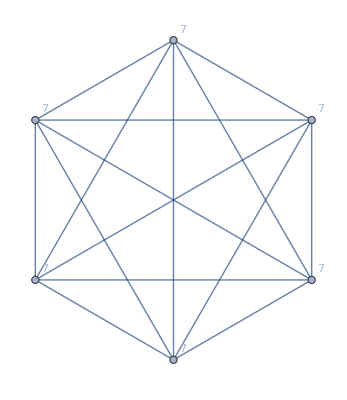
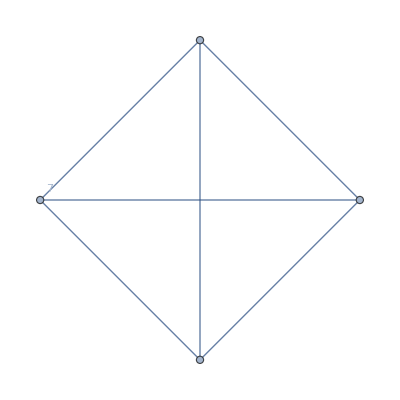
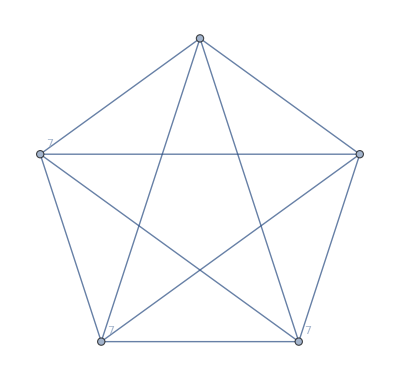
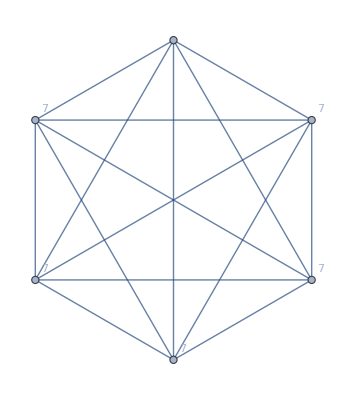
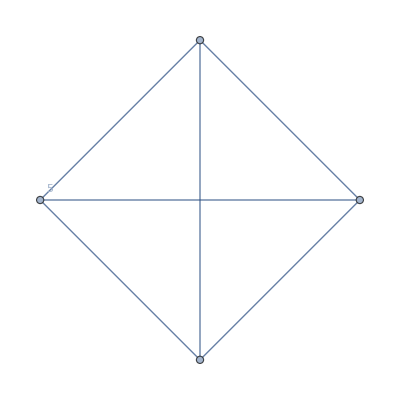
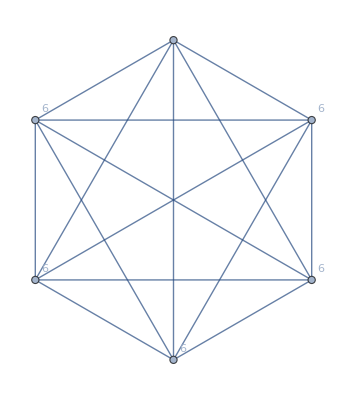
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComputeGraph[Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->6,3<->6,4<->6,5<->6,7<->6,7<->2,7<->5,7<->1}],Table[{k},{k,7}]]
```